```mathematica
Integrate[Cos[m x]^2,{x,0,π}]
```

(2 m π+Sin[2 m π])/(4 m)

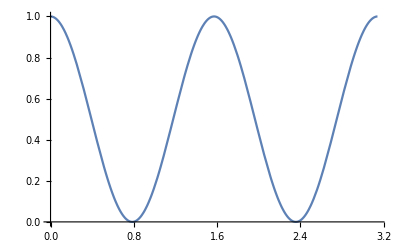

```mathematica
Plot[Cos[2 x]^2,{x,0,3.14}]
```

```mathematica
(26(26+1))/2+26-26-1
```

350

```mathematica
BenchMark
```

```mathematica
pilist=RealDigits[√2,10,10000000][[1]];
```

```mathematica
Counts[pilist]
```

<|3→100230,1→99757,4→100230,5→100359,9→100106,2→100026,6→99548,8→99985,7→99800,0→99959|>

```mathematica
SequenceCount[pilist,{6,4,6,6,9,4}]
```

9

```mathematica
Interpreter["TeXExpression"] ["\\frac{(D-1)(D-2)D}{6}+3(D-1)D+D+\\frac{D^2+D}{2}+D-D-\\frac{D^2+D}{2}-D-1"]
```

```mathematica
-1+3 (-1+D) D+1/6 (-2+D) (-1+D) D+1/2 (-D-D^2)+1/2 (D+D^2)//FullSimplify
```

-1+1/6 (-1+D) D (16+D)

```mathematica
-1+1/6 (-1+D) D (16+D)/.{D->26}
```

4549

```mathematica
FourierTransform[1/x,x,k]
```

FourierTransform[1/(x Log[x]),x,k]